```mathematica
<<"F:\\时间序列分析\\own_ts.m"
```

此函数包有wmn7制作,可供大家自由学习

函数名称 | 要点 | 参数使用
swpacf | 给出自相关图和偏自相关图 | swpacf[数据,最大滞后数,置信度]
whiteNoiseTest | 白噪声检验 | whiteNoiseTest[数据]
seadiff | 季节差分 | seadiff[数据,季节数]
arimafix | 拟合模型 | arimafix[数据,(ar,差分,ma),季节里的(ar,差分,ma),季节数,是否有固定系数]
css | 结合arimafix使用,将arimafix函数返回的数据用表格的形式呈现 | css[arimafix[...]]
Arima | 带有drift项,一般与forecast合用 | Arima[数据,(ar,差分,ma),季节里的(ar,差分,ma),季节数]
Arimafix | 带有drift项,与Arima相比,可以输入稀疏系数 | Arimafix[数据,(ar,差分,ma),季节里的(ar,差分,ma),季节数,是否有固定系数]
CSS | 结合Arimafix使用,将arimafix函数返回的数据用表格的形式呈现 | CSS[Arimafix[...]]
forecast | 给出预测,结合forecastPlot使用 | 会自动使用你上面预测用得模型,forecast[数据,(ar,差分,ma),季节里的(ar,差分,ma),季节数,往后预测个数],..[[1,4,1]]可以得到预测的具体数值
residualAnalysis | 对forecast得到的模型进行残差分析 | residualAnalysis[model],其中model为使用forecast返回的模型
forecastFix | 给出预测,结合forecastPlot使用 | 会自动使用你上面预测用得模型,forecast[数据,(ar,差分,ma),季节里的(ar,差分,ma),季节数,是否有固定系数,往后预测个数]
forecastPlot | 画出预测图像,结合forecast使用 | forecastPlot[forecast返回值,原始数据]
forecastPlotNDate | 画出预测图像,只包含预测的数据和区间,结合forecast使用 | forecastPlot[forecast返回值,原始数据]
forecastTable | 以表格的形式给出预测数据和置信区间的数据 | forecastTable[forecast返回值]

```mathematica
data = {977.5,892.5,942.3,941.3,962.2,1005.7,963.8,959.8,1023.3,1051.1,1102.,1415.5,1192.2,1162.7,1167.5,1170.4,1213.7,1281.1,1251.5,1286.,1396.2,1444.1,1553.8,1932.2,1602.2,1491.5,1533.3,1548.7,1585.4,1639.7,1623.6,1637.1,1756.,1818.,1935.2,2389.5,1909.1,1911.2,1860.1,1854.8,1898.3,1966.,1888.7,1916.4,2083.5,2148.3,2290.1,2848.6,2288.5,2213.5,2130.9,2100.5,2108.2,2164.7,2102.5,2104.4,2239.6,2348.,2454.9,2881.7,2549.5,2306.4,2279.7,2252.7,2265.2,2326.,2286.1,2314.6,2443.1,2536.,2652.2,3131.4,2662.1,2538.4,2403.1,2356.8,2364.,2428.8,2380.3,2410.9,2604.3,2743.9,2781.5,3405.7,2774.7,2805.,2627.,2572.,2637.,2645.,2597.,2636.,2854.,3029.,3108.,3680.};
```

```mathematica
(*画出数据的时间序列图*)
```

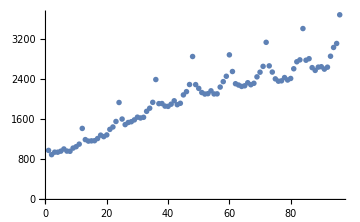

```mathematica
p = ListPlot[Flatten@data,ImageSize->Medium]
```

```mathematica
(*求出数据的自相关和偏自相关图*)
```

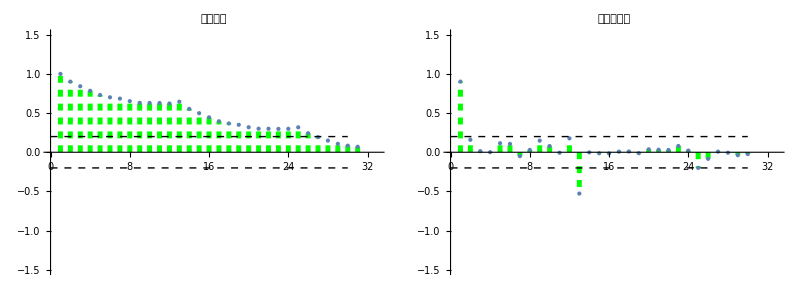

```mathematica
swpacf[data,30,.95]
```

```mathematica
(*进行一阶差分*)
```

```mathematica
datadiff = Differences[data];
```

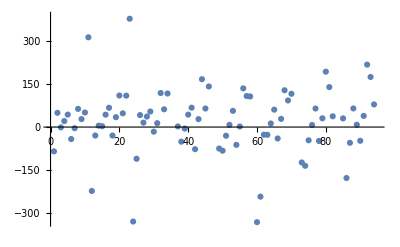

```mathematica
ListPlot[datadiff]
```

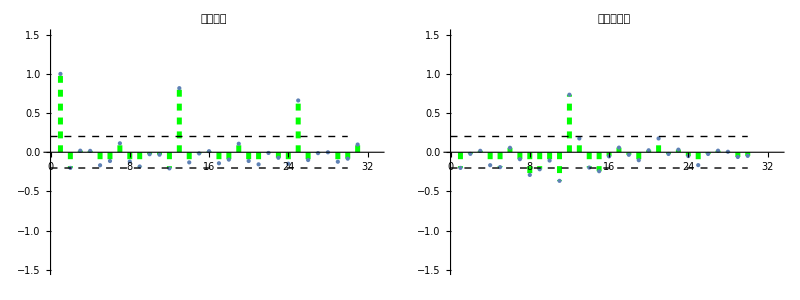

```mathematica
swpacf[datadiff,30,.95]
```

```mathematica
(*从上面的图中可以看到有周期性质，周期为 D=12 *)
```

```mathematica
datadiffSeadiff = seadiff[datadiff,12];
```

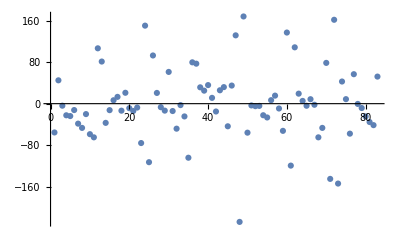

```mathematica
ListPlot[datadiffSeadiff]
```

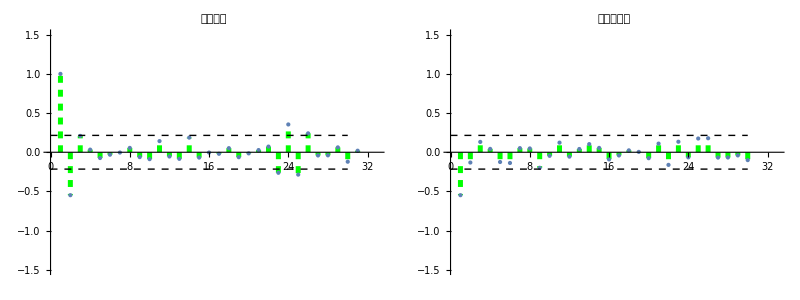

```mathematica
swpacf[datadiffSeadiff,30,.95]
```

```mathematica
(*拟合模型，查看模型的好坏*)
```

```mathematica
m = Arima[data,"c(1,1,1)","c(0,1,0)","12"];
CSS[m]
```

| ar1 | ma1
参数 | -0.449322 | -0.148779
标准差 | 0.152686 | 0.156522
模型的方差 | 3191.84 | 
极大似然估计 | -451.784 | 
AIC | 909.567 | 
AICc | 909.871 | 
BIC | 916.824 |

```mathematica
(*画出模型的预测图*)
```

```mathematica
fore = forecast[data,"c(1,1,1)","c(0,1,0)","12","24"];
```

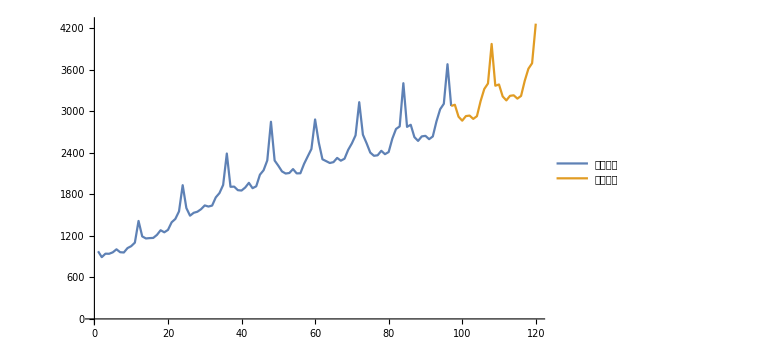
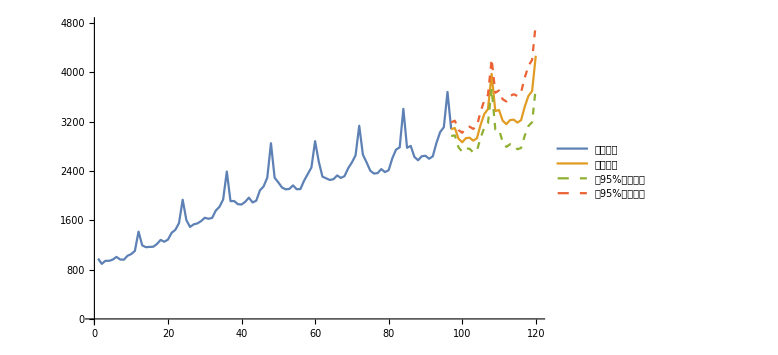

```mathematica
forecastPlot[fore,data]
```

```mathematica
(*只画出预测部分*)
```

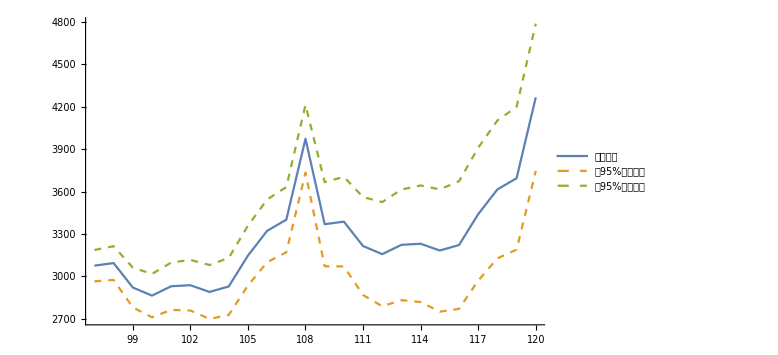

```mathematica
forecastPlotNData[fore,data]
```

```mathematica
(*进行残差分析*)
```

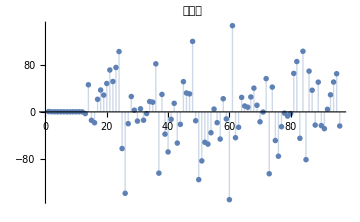

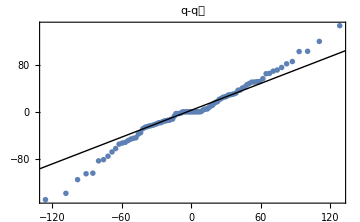
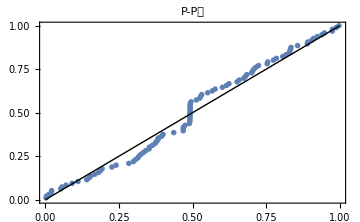

白噪声检验:

| Statistic | P-Value
Box-Pierce | 4.94051 | 0.423184
Ljung-Box | 5.2524 | 0.38586

```mathematica
residualAnalysis[fore]
```

```mathematica
(*以表格形式给出预测值的大小*)
```

```mathematica
forecastTable[fore]
```

预测数据 | 下80%置信区间 | 上80%置信区间 | 下95%置信区间 | 上95%置信区间
3076.02 | 3003.61 | 3148.42 | 2965.29 | 3186.75
3094.18 | 3016.15 | 3172.21 | 2974.84 | 3213.52
2921.63 | 2829.73 | 3013.54 | 2781.08 | 3062.19
2864.18 | 2764.02 | 2964.34 | 2711. | 3017.36
2930.28 | 2820.99 | 3039.58 | 2763.13 | 3097.43
2937.79 | 2820.71 | 3054.87 | 2758.73 | 3116.84
2890.01 | 2765.37 | 3014.66 | 2699.38 | 3080.64
2928.91 | 2797.25 | 3060.57 | 2727.55 | 3130.27
3146.96 | 3008.58 | 3285.33 | 2935.33 | 3358.58
3321.94 | 3177.18 | 3466.69 | 3100.55 | 3543.32
3400.94 | 3250.07 | 3551.82 | 3170.2 | 3631.69
3972.94 | 3816.19 | 4129.69 | 3733.21 | 4212.67
3368.96 | 3174.59 | 3563.33 | 3071.7 | 3666.22
3387.12 | 3179.97 | 3594.27 | 3070.32 | 3703.92
3214.57 | 2988.29 | 3440.86 | 2868.5 | 3560.65
3157.12 | 2916.32 | 3397.92 | 2788.85 | 3525.4
3223.22 | 2967.44 | 3479.01 | 2832.03 | 3614.42
3230.73 | 2961.35 | 3500.11 | 2818.74 | 3642.71
3182.95 | 2900.39 | 3465.52 | 2750.81 | 3615.1
3221.85 | 2926.8 | 3516.91 | 2770.61 | 3673.1
3439.9 | 3132.82 | 3746.98 | 2970.26 | 3909.54
3614.88 | 3296.24 | 3933.51 | 3127.57 | 4102.18
3693.89 | 3364.09 | 4023.68 | 3189.51 | 4198.26
4265.88 | 3925.3 | 4606.46 | 3745.01 | 4786.75